```mathematica
ass=Assumptions->{kx,ky,kz,k,θ,χ,ϕ,θp,ϕp,kp,cq,vf,B,μ,chi,fac} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && βtra>0 && βter>0 && cq>=0 && vf>0 && B>0;
```

## Computing W_kk'

```mathematica
σ1=PauliMatrix[1];σ2=PauliMatrix[2];σ3=PauliMatrix[3];
Clear[ham];
ham[χ_]=kx σ1+ky σ2+ χ kz σ3;
FullSimplify[FullSimplify[Eigensystem[ham[χ]]/.χ^2->1,ass]/.rep,ass]

hamc[χ_]= χ (kx σ1+ky σ2+kz σ3);
FullSimplify[FullSimplify[Eigensystem[hamc[χ]]/.χ^2->1,ass]/.rep,ass]
```

{{-k,k},{{(ⅇ^(-ⅈ ϕ) (-1+χ Cos[θ]))/Sin[θ],1},{ⅇ^(-ⅈ ϕ) (χ Cot[θ]+1/Sin[θ]),1}}}

{{-k χ,k χ},{{-ⅇ^(-ⅈ ϕ) Tan[θ/2],1},{ⅇ^(-ⅈ ϕ) Cot[θ/2],1}}}

```mathematica
Clear[vec,vecdag];
vec[χ_,θ_,ϕ_]=Sin[θ]{ⅇ^(-ⅈ ϕ) (χ Cot[θ]+1/Sin[θ]),1}//FullSimplify;
vecdag[χ_,θ_,ϕ_]=Sin[θ]{ⅇ^(ⅈ ϕ) (χ Cot[θ]+1/Sin[θ]),1}//FullSimplify;
norm=FullSimplify[√((vecdag[χ,θ,ϕ].vec[χ,θ,ϕ]//Expand)/.χ^2->1),ass]
v[χ_,θ_,ϕ_]=FullSimplify[vec[χ,θ,ϕ]/norm,ass]
vdag[χ_,θ_,ϕ_]=FullSimplify[vecdag[χ,θ,ϕ]/norm,ass]
```

√(2+2 χ Cos[θ])

{(ⅇ^(-ⅈ ϕ) √(1+χ Cos[θ]))/(√2),Sin[θ]/(√(2+2 χ Cos[θ]))}

{(ⅇ^(ⅈ ϕ) √(1+χ Cos[θ]))/(√2),Sin[θ]/(√(2+2 χ Cos[θ]))}

```mathematica
Clear[vecp];
vecp[χ_,θ_,ϕ_]={(ⅇ^(-ⅈ ϕ) √(1+χ Cos[θ]))/(√2),Sin[θ]/(√(2+2 χ Cos[θ]))};
vecpdag[χ_,θ_,ϕ_]={(ⅇ^(ⅈ ϕ) √(1+χ Cos[θ]))/(√2),Sin[θ]/(√(2+2 χ Cos[θ]))};
chi=1;
FullSimplify[vintra^2/(2π) Integrate[(vecpdag[chi,θ,ϕ].vecp[chi,θp,ϕp])(vecpdag[chi,θp,ϕp].vecp[chi,θ,ϕ]),{ϕp,0,2π}],ass]
vinter^2 FullSimplify[Integrate[((vecpdag[chi,θ,ϕ].vecp[-chi,θp,ϕp])(vecpdag[-chi,θp,ϕp].vecp[chi,θ,ϕ]))/(2π),{ϕp,0,2π}],ass]

chi=-1;
vintra^2 FullSimplify[Integrate[((vecpdag[chi,θ,ϕ].vecp[chi,θp,ϕp])(vecpdag[chi,θp,ϕp].vecp[chi,θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
vinter^2 FullSimplify[Integrate[((vecpdag[chi,θ,ϕ].vecp[-chi,θp,ϕp])(vecpdag[-chi,θp,ϕp].vecp[chi,θ,ϕ]))/(2π),{ϕp,0,2π}],ass]
```

1/2 vintra^2 (1+Cos[θ] Cos[θp])

1/2 vinter^2 (1-Cos[θ] Cos[θp])

1/2 vintra^2 (1+Cos[θ] Cos[θp])

1/2 vinter^2 (1-Cos[θ] Cos[θp])

## Initial definitions

```mathematica
AugmentedMatrix[{},vars_]:={}
AugmentedMatrix[matA_List==matB_List,vars_]:=AugmentedMatrix[matA-matB,vars]
AugmentedMatrix[mat_,vars_]:=
With[{temp=CoefficientArrays[Flatten[Thread/@mat],vars]},Normal[Transpose[Join[Transpose[temp[[2]]],-{temp[[1]]}]]]]
AugmentedMatrix[{Subscript[a, 11] Subscript[x, 1]+Subscript[a, 12] Subscript[x, 2]-Subscript[b, 1]==0,Subscript[a, 21] Subscript[x, 1]+Subscript[a, 22] Subscript[x, 2]-Subscript[b, 2]==0},{Subscript[x, 1],Subscript[x, 2]}]//MatrixForm
repl={Cos[θ]->cost,Sin[θ]->sint,Sin[ϕ]->sphi,Cos[ϕ]->cphi};
```

(a_11 | a_12 | b_1
a_21 | a_22 | b_2)

```mathematica
Clear[Λ,lhs,rhs,λ,c];
rep={a[1]->ap, a[-1]->am,b[1]->bp, b[-1]->bm,λ[1]->λp, λ[-1]->λm,β[1,1]->βintra,β[-1,-1]->βintra,β[1,-1]->βinter,β[-1,1]->βinter};

Λ[χ_,θ_]=(* remove minus sign and compensate *) τ[χ,θ](λ[χ]-h[χ,θ] + a[χ] Cos[θ]+c);
G[χ_, η_]=1+χ η Cos[θ] Cos[θp];

lhs[χ_,θ_]=h[χ,θ]+(* remove minus sign and compensate *) Λ[χ,θ]/τ[χ,θ]//Simplify

rhs[χ_,θ_]=β[χ,1]intθp f[1,θp] G[χ,1](λ[1]-h[1,θp] + a[1] Cos[θp]+c)+β[χ,-1]intθp f[-1,θp]G[χ,-1](λ[-1]-h[-1,θp] + a[-1] Cos[θp]+c);

chi=1;
eqn1=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,0}]/.rep//Simplify;
eqn2=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,1}]/.rep//Simplify;
chi=-1;
eqn3=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,0}]/.rep//Simplify;
eqn4=SeriesCoefficient[(lhs[chi,θ]-rhs[chi,θ]/.repl),{cost,0,1}]/.rep//Simplify;
eqn5=intθp(f[1,θp]Λ[1,θp]+f[-1,θp]Λ[-1,θp])/.rep//Simplify
```

c+a[χ] Cos[θ]+λ[χ]

intθp (f[-1,θp] (c+λm+am Cos[θp]-h[-1,θp]) τ[-1,θp]+f[1,θp] (c+λp+ap Cos[θp]-h[1,θp]) τ[1,θp])

```mathematica
(* https://resources.wolframcloud.com/FunctionRepository/resources/AugmentedMatrix/ *)
```

## matrices

```mathematica
amat//MatrixForm;
arr=CoefficientArrays[{eqn1==0,eqn2==0,eqn3==0,eqn4==0},{λp,ap,λm,am}];
array=Normal[arr]//Simplify;
cmat=array[[2]]//Simplify;
cmat//MatrixForm
array[[1]]//MatrixForm
MatrixRank[amat]
MatrixRank[cmat]
```

(1-intθp βintra f[1,θp] | -intθp βintra Cos[θp] f[1,θp] | -intθp βinter f[-1,θp] | -intθp βinter Cos[θp] f[-1,θp]
-intθp βintra Cos[θp] f[1,θp] | 1-intθp βintra Cos[θp]^2 f[1,θp] | intθp βinter Cos[θp] f[-1,θp] | intθp βinter Cos[θp]^2 f[-1,θp]
-intθp βinter f[1,θp] | -intθp βinter Cos[θp] f[1,θp] | 1-intθp βintra f[-1,θp] | -intθp βintra Cos[θp] f[-1,θp]
intθp βinter Cos[θp] f[1,θp] | intθp βinter Cos[θp]^2 f[1,θp] | -intθp βintra Cos[θp] f[-1,θp] | 1-intθp βintra Cos[θp]^2 f[-1,θp])

(c+intθp βinter f[-1,θp] (-c+h[-1,θp])+intθp βintra f[1,θp] (-c+h[1,θp])
intθp Cos[θp] (βinter f[-1,θp] (c-h[-1,θp])+βintra f[1,θp] (-c+h[1,θp]))
c+intθp βintra f[-1,θp] (-c+h[-1,θp])+intθp βinter f[1,θp] (-c+h[1,θp])
intθp Cos[θp] (βintra f[-1,θp] (-c+h[-1,θp])+βinter f[1,θp] (c-h[1,θp])))

4

4

```mathematica
c=0;
sol=Flatten[Solve[{eqn1==0,eqn3==0,eqn2==0,eqn4==0},{ap,am,λp,λm}]//FullSimplify,1]
Clear[c];
```

```mathematica
{nap,nam,nλp,nλm}={Numerator[ap/.sol],Numerator[am/.sol],Numerator[λp/.sol],Numerator[λm/.sol]};
```

```mathematica
{dap,dam,dλp,dλm}={Denominator[ap/.sol],Denominator[am/.sol],Denominator[λp/.sol],Denominator[λm/.sol]};
{dap==dam,dap==dλp,dap==dλm}
dap
```

{True,True,True}

8-4 intθp βintra (3+Cos[2 θp]) f[1,θp]+intθp f[-1,θp] (-4 βintra (3+Cos[2 θp])+intθp (-3 βinter^2+19 βintra^2+4 (βinter^2+3 βintra^2) Cos[2 θp]+(-βinter^2+βintra^2) Cos[4 θp]) f[1,θp])

## phys quantities

```mathematica
rep={kx->k Sin[θ] Cos[ϕ],ky->k Sin[θ] Sin[ϕ],kz->k Cos[θ]};
ass=Assumptions->{kx,ky,kz,k,θ,χ,ϕ,θp,ϕp,kp,vinter,vinter} ∈ Reals && k>0 && kp>0 && 0<=θ<=π && 0<=θp<=π && vintra>0 && vinter>0;v0=FullSimplify[{D[vf √(kx^2+ky^2+kz^2),kx],D[vf √(kx^2+ky^2+kz^2),ky],D[vf √(kx^2+ky^2+kz^2),kz]}/.rep,ass]
v0dotk=FullSimplify[%.{kx,ky,kz}/.rep,Assumptions->k ∈ Reals && k>0]
D[(χ e vf kz B)/(2(kx^2+ky^2+kz^2)) ,kz]/.rep//FullSimplify
```

{vf Cos[ϕ] Sin[θ],vf Sin[θ] Sin[ϕ],vf Cos[θ]}

k vf

-(B e vf χ Cos[2 θ])/(2 k^2)

```mathematica
(* ϵm =(χ e vf k Cos[θ] B)/(2 k^2) *)
vm=FullSimplify[{D[(χ e vf kz B)/(2(kx^2+ky^2+kz^2)) ,kx],D[(χ e vf kz B)/(2(kx^2+ky^2+kz^2)) ,ky],D[(χ e vf kz B)/(2(kx^2+ky^2+kz^2)) ,kz]},ass]
vmdotk=FullSimplify[%.{kx,ky,kz}/.rep,ass]
```

{-(B e kx kz vf χ)/((kx^2+ky^2+kz^2)^2),-(B e ky kz vf χ)/((kx^2+ky^2+kz^2)^2),(B e (kx^2+ky^2-kz^2) vf χ)/(2 (kx^2+ky^2+kz^2)^2)}

-(B e vf χ Cos[θ])/(2 k)

```mathematica
chi 4 Cos[θp](e B vf^2)/(2 μ^2)
```

(2 B chi e vf^2 Cos[θp])/μ^2

## sigma

```mathematica
Clear[sig];
sig[B_,βintra_,βinter_]:=Block[{e=1,μ=0.1,vf=0.005,c=0,matr,rhs1,rhs2,θ,τ1,τ2,kf1,kf2,f1,f2,vdotk1,vdotk2,α,conteq,λ1,λ2,a1,a2,cost,θp,chi,Dphase1,Dphase2,h1,vz1,h2,vz2,zero1,zero2,ct1,ct2,ctct1,ctct2,hzero1,hzero2,hct1,hct2,hstcp1,hstcp2,hstsp1,hstsp2,colvec,mat,sol,Λ1,Λ2,s1,s2,int1,int2},
α=(e B vf^2)/(2 μ^2);
chi=1;
kf1[θp_]= μ/(2vf)(1+√(1-chi 4 α Cos[θp])) ;
Dphase1[θp_]=1 +e(-chi Cos[θp] B)/(2(kf1[θp])^2);
vz1[θp_]=vf Cos[θp]-(e B  vf chi Cos[2 θp])/(2 (kf1[θp])^2);
vdotk1[θp_]=kf1[θp] vf-(B e vf chi Cos[θp])/(2 kf1[θp]);
h1[θp_]=1/Dphase1[θp](vz1[θp]+e B (vf chi (-2 (kf1[θp])^2+B e chi Cos[θp]))/(4 (kf1[θp])^4) );
(*******************)
chi=-1;
Dphase2[θp_]=1 +e(-chi Cos[θp] B)/(2(kf2[θp])^2);
kf2[θp_]= μ/(2vf)(1+√(1-chi 4 α Cos[θp])) ;
vz2[θp_]=vf Cos[θp]-(e B  vf chi Cos[2 θp])/(2 (kf2[θp])^2);
vdotk2[θp_]=kf2[θp] vf-(B e vf chi Cos[θp])/(2 kf2[θp]);
h2[θp_]=1/Dphase2[θp](vz2[θp]+e B (vf chi (-2 (kf2[θp])^2+B e chi Cos[θp]))/(4 (kf2[θp])^4) );
τ1[θ_]=(βintra NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]+
βintra   Cos[θ] NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp]Cos[θp],{θp,0,π}]+βinter NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]- Cos[θ] βinter NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;
τ2[θ_]=(βinter NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp],{θp,0,π}]- Cos[θ]βinter NIntegrate [(Sin[θp] (kf1[θp])^3)/Abs[vdotk1[θp]] Dphase1[θp] Cos[θp],{θp,0,π}]+βintra NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp],{θp,0,π}]+ Cos[θ] βintra NIntegrate [(Sin[θp] (kf2[θp])^3)/Abs[vdotk2[θp]] Dphase2[θp]Cos[θp],{θp,0,π}])^-1;

f1[θ_]=(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]] Dphase1[θ] τ1[θ];
f2[θ_]=(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]] Dphase2[θ] τ2[θ];
zero1=Quiet[NIntegrate [f1[θp],{θp,0,π}]];
zero2=Quiet[NIntegrate [f2[θp],{θp,0,π}]];
ct1=Quiet[NIntegrate [f1[θp] Cos[θp],{θp,0,π}]];
ct2=Quiet[NIntegrate [f2[θp] Cos[θp],{θp,0,π}]];
ctct1=Quiet[NIntegrate [f1[θp] Cos[θp]^2,{θp,0,π}]];
ctct2=Quiet[NIntegrate [f2[θp] Cos[θp]^2,{θp,0,π}]];

hzero1=Quiet[NIntegrate [f1[θp] h1[θp],{θp,0,π}]];
hzero2=Quiet[NIntegrate [f2[θp]h2[θp],{θp,0,π}]];
hct1=Quiet[NIntegrate [f1[θp]h1[θp]Cos[θp],{θp,0,π}]];
hct2=Quiet[NIntegrate [f2[θp]h2[θp]Cos[θp],{θp,0,π}]];

colvec=({{βintra hzero1+βinter hzero2}, {βintra hct1-βinter hct2}, {βintra hzero2+βinter hzero1}, {βintra hct2-βinter hct1}});
matr=({{1-βintra zero1, -βintra ct1, -βinter zero2, -βinter ct2}, {-βintra ct1, 1-βintra ctct1, βinter ct2, βinter ctct2}, {-βinter zero1, -βinter ct1, 1-βintra zero2, -βintra ct2}, {βinter ct1, βinter ctct1, -βintra ct2, 1-βintra ctct2}});
(*sol=LinearSolve[mat,-colvec]//Chop;*)
mat=matr.{λ1,a1,λ2,a2};
conteq=(λ1 zero1-hzero1+a1 ct1)+(λ2 zero2-hzero2+a2 ct2);

sol=Flatten[Solve[{mat[[1]]+colvec[[1]]==0,mat[[2]]+colvec[[2]]==0,mat[[3]]+colvec[[3]]==0,mat[[4]]+colvec[[4]]==0,conteq==0},{λ1,a1,λ2,a2}],1]//Chop;

Λ1[θ_]=τ1[θ](λ1-h1[θ]+a1 Cos[θ])/.sol;
Λ2[θ_]=τ2[θ](λ1-h1[θ]+a1 Cos[θ])/.sol;

(* -Graphics- *)
int1[θ_]=-(Sin[θ] (kf1[θ])^3)/Abs[vdotk1[θ]]e(vz1[θ]+e B(vf (-2 kf1[θ]^2+B e  Cos[θ]))/(4 kf1[θ]^4) )Λ1[θ];
int2[θ_]=-(Sin[θ] (kf2[θ])^3)/Abs[vdotk2[θ]]e(vz2[θ]+e B(-vf (-2 kf2[θ]^2-B e  Cos[θ]))/(4 kf2[θ]^4))Λ2[θ];

s1=NIntegrate[int1[θ],{θ,0,π}];
s2=NIntegrate[int2[θ],{θ,0,π}];
{α,s1+s2,MatrixForm[{λ1,a1,λ2,a2}/.sol],Chop[c],MatrixRank[matr]}
];
sig[10,1,0.5]
```

{0.0125,0.000012497,(0.0000260428
-0.000624966
-0.0000260428
-0.000624966),0,3}

{{0.000125,4.16667×10^-6},{0.001375,4.16665×10^-6},{0.002625,4.16662×10^-6},{0.003875,4.16657×10^-6},{0.005125,4.1665×10^-6},{0.006375,4.1664×10^-6},{0.007625,4.16629×10^-6},{0.008875,4.16616×10^-6},{0.010125,4.166×10^-6},{0.011375,4.16583×10^-6}}

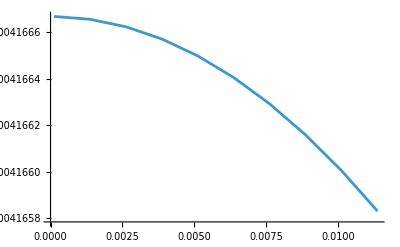

```mathematica
vintra=3;vinter=vintra/2;
dat1=Table[Quiet[sig[B,vintra,vinter]],{B,0.1,10,1}];
list=dat1;
len=Length[list];
scale=1(*list[[1,2]]*);
dat=Table[{list[[i,1]],list[[i,2]]scale},{i,1,len}]
ListLinePlot[{dat}]
```